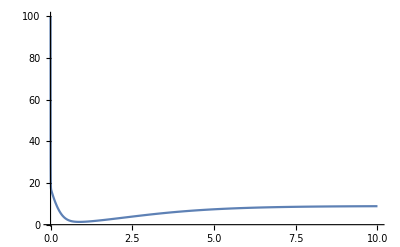

```mathematica
Clear["Global`*"];
k1=10;
k2=0.01;
k3=1;
k4=0.01;
k5=10;
k6=100;
k7=0.1;
k8=100;
k9=0.01;
k10=0.01;
k11=1;
sTot=84614.84435;
eTot=3504.020816;
DAE=({{x1'[t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t]}, {x2'[t]==k3*x5[t]+k6*x6[t]-k7*x2[t]}, {x3'[t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t]}, {x4'[t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t]}, {x5'[t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t]}, {x6'[t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]}});

x1i=100;
x2i=0;
x3i=100;
x4i=0;
x5i=0;
x6i=0;

(*x5i=(sTot-xli)/3; x6i=(sTot-xli)/3;x2i=sTot-(x1i+x5i+x6i);*)
sol=NDSolve[{DAE,x1[0]==x1i,x2[0]==x2i,x3[0]==x3i,x4[0]==x4i,x5[0]==x5i,x6[0]==x6i},{x1},{t,0,1000}];

Plot[Evaluate[{x1[t],x3[t]}/.sol],{t,0,10},PlotRange->All]
```